```mathematica
dataZ=sToZ[TSData];
```

```mathematica
dataZF=freqAppend[dataZ];
```

```mathematica
fmin=500 10^6;
fmax=1000 10^6;
dataZFroi=Select[dataZF,#[[1]]>fmin&&#[[1]]<fmax&];
dataZroi=dataZFroi[[;;,2]];
```

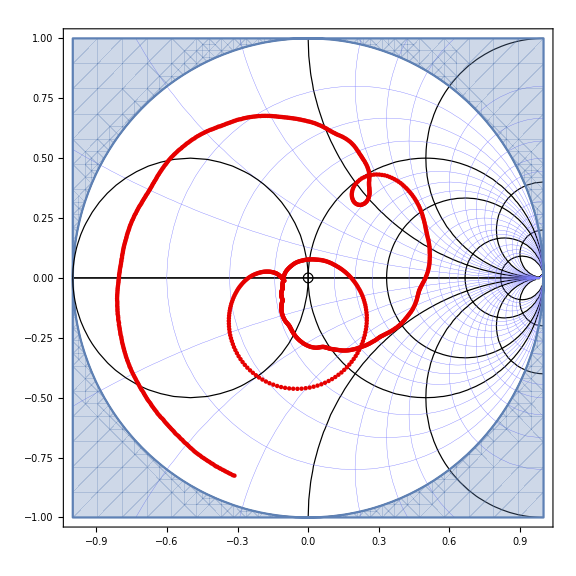

```mathematica
SmithChartListPlot[dataZroi//Flatten]
```

```mathematica
par[a_,b_]:=a b/(a+b)
ZTuning[zl_,z1_,z2_,z3_]:=par[par[zl,z3]+z2,z1]
ZTuningLPS[zl_,z2_,z3_]:=par[zl,z3]+z2
ZTuningLSP[zl_,z1_,z2_]:=par[zl+z2,z1]
```

```mathematica
ZTuningF[zlf_,z1f_,z2f_,z3f_]:=ZTuning[#[[2]][[1]],N[z1f/.f->#[[1]]],N[z2f/.f->#[[1]]],N[z3f/.f->#[[1]]]]&/@zlf
```

```mathematica
ZTuningFLPS[zlf_,z2f_,z3f_]:=ZTuningLPS[#[[2]][[1]],N[z2f/.f->#[[1]]],N[z3f/.f->#[[1]]]]&/@zlf
ZTuningFLSP[zlf_,z1f_,z2f_]:=ZTuningLPS[#[[2]][[1]],N[z1f/.f->#[[1]]],N[z2f/.f->#[[1]]]]&/@zlf
```

```mathematica
ZTuningF[zlf_,z1f_,z2f_,z3f_]:=ZTuning[#[[2]][[1]],N[z1f/.f->#[[1]]],N[z2f/.f->#[[1]]],N[z3f/.f->#[[1]]]]&/@zlf
```

```mathematica
Manipulate[SmithChartListPlot[ZTuningF[dataZFroi,1/(I 2Pi f cc),10^9,10^9]],{cc,10^-12,20 10^-12}];
```

```mathematica
ZtunedLoLC=ZTuningF[dataZFroi,10^12,1/(I 2 Pi f c),I 2 Pi f l][[1]]
```

-((0.+3.17992×10^-10 ⅈ) (1.×10^12+((1.07902×10^11+1.44211×10^10 ⅈ) l)/((4.5858-34.312 ⅈ)+(0.+3.14473×10^9 ⅈ) l)))/(c (1.×10^12-(0.+3.17992×10^-10 ⅈ)/c+((1.07902×10^11+1.44211×10^10 ⅈ) l)/((4.5858-34.312 ⅈ)+(0.+3.14473×10^9 ⅈ) l)))